一個隨機抽卡的遊戲

假設有3人參加比賽, 底分為 0.
有3張寫上 +1, 0, -1 的卡

每一輪每人獲分派一張卡.

請問: 第 N 輪以後, 最高分的人的 Expected Value 是多少分數?

Bonus: 如果有 K 人比賽, 有K 張卡, 情況會如何?
(如果 K = even, 請把卡當成是 ... -1.5, -0.5, +0.5, +1.5,..... )

## Method 1 (bull force)

```mathematica
(* Check the algrithm of suming *)Table[{k1,k2,3-k1-k2},{k1,0,3},{k2,0,3-k1}]//TableForm
```

0
0
3 | 0
1
2 | 0
2
1 | 0
3
0
1
0
2 | 1
1
1 | 1
2
0 | 
2
0
1 | 2
1
0 |  | 
3
0
0 |  |  |

```mathematica
(* Expected Win For 3*)
(* ki is the number of Win for the i-th people *)
(* n is the total number of draw *)
(* Because when the i-th people win, ki times, the Maximum one is the winner, so, Max[ k1, k2, n- k1-k2 ] is the winner price *)EX[n_]:=Sum[(n!)/(k1! k2!(n-k1-k2)!)Max[k1,k2,n-k1-k2],{k1,0,n},{k2,0,n-k1}]/3^n
```

```mathematica
Table[N[Sum[(n!)/(k1! k2!(n-k1-k2)!)Max[k1,k2,n-k1-k2],{k1,0,n},{k2,0,n-k1}]/3^n],{n,1,60}]
```

{1.,1.33333,1.88889,2.37037,2.77778,3.23457,3.67764,4.07499,4.50434,4.92659,5.31753,5.73171,6.14155,6.52762,6.93199,7.33337,7.71564,8.11301,8.50818,8.88737,9.27944,9.6698,10.0464,10.4343,10.8208,11.1953,11.5798,11.9631,12.3357,12.7173,13.0979,13.469,13.8481,14.2264,14.5961,14.9731,15.3494,15.7178,16.093,16.4675,16.8347,17.2083,17.5813,17.9474,18.3195,18.6911,19.0564,19.4271,19.7975,20.1618,20.5314,20.9006,21.2642,21.6327,22.0008,22.3636,22.7312,23.0983,23.4605,23.8271}

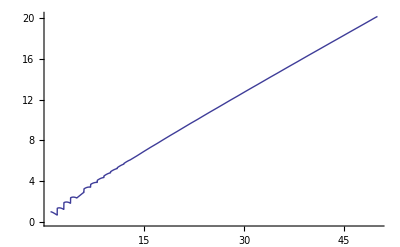

```mathematica
Plot[{Sum[(n!)/(k1! k2!(n-k1-k2)!)Max[k1,k2,n-k1-k2],{k1,0,n},{k2,0,n-k1}]/3^n},{n,1,50}]
```

```mathematica
A={
{1,0},
{0,1},
{-1,0},
{0,-1}};
```

```mathematica
Table[Max[A[[i]]+A[[j]]],{i,1,4},{j,1,4}];
%//TableForm
```

2 | 1 | 0 | 1
1 | 2 | 1 | 0
0 | 1 | 0 | -1
1 | 0 | -1 | 0

```mathematica
(* Game of 4 *)EA[n_]:=Sum[(n!)/(k1!k2!k3!(n-k1-k2-k3)!)Max[k1 A[[1]]+k2 A[[2]]+k3 A[[3]]+(n-k1-k2-k3) A[[4]]],{k1,0,n},{k2,0,n-k1},{k3,0,n-k1-k2}]/4^n
```

```mathematica
EA[5]
```

15/16

```mathematica
T=Permutations[{1,0,-1}];(* Generate all possible outcome from {1,0,-1} *)
a=Length[T] (* find the number of outcome *)
Array[k,a] (* Claim ki *)
(* Expected Win of the winner *)
ES[n_]:=Sum[(n!)/(Product[k[i]!,{i,1,a-1}](n-Sum[k[i],{i,1,a-1}])!)Max[Sum[k[j]T[[j]],{j,1,a-1}]+(n-Sum[k[i],{i,1,a-1}])*T[[a]]],
{k[1],0,n},
{k[2],0,n-k[1]},
{k[3],0,n-k[1]-k[2]},
{k[4],0,n-k[1]-k[2]-k[3]},
{k[5],0,n-k[1]-k[2]-k[3]-k[4]}]/a^n
```

6

```mathematica
Table[N[ES[i]],{i,1,20}]
```

{1.,1.16667,1.5,1.69444,1.90586,2.07948,2.24751,2.40025,2.54556,2.68222,2.81264,2.9371,3.05659,3.17154,3.2825,3.38981,3.49384,3.59486,3.69312,3.78883}

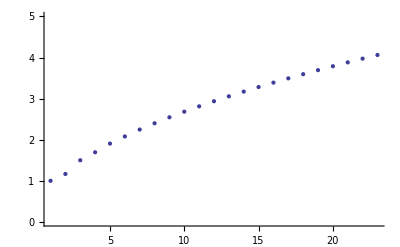

```mathematica
ListPlot[{1.,1.1666666666666667,1.5,1.6944444444444444,1.9058641975308641,2.0794753086419755,2.247513717421125,2.4002486282578874,2.545556841563786,2.682217244894071,2.812637928351877,2.937098420115074,3.056588314762951,3.1715418112739897,3.2824956811238413,3.3898126121175065,3.493841582870599,3.5948607801899946,3.6931203020419514,3.7888330192638136,3.882187944949646,3.973350754795889,4.062469113674849},PlotRange->{0,5}]
```

## Method 2 (vector space)

## Method 3 ( irtaration )

```mathematica
Permutations[{1,0,-1}](* Generate all possible outcome from {1,0,-1} *)
```

{{1,0,-1},{1,-1,0},{0,1,-1},{0,-1,1},{-1,1,0},{-1,0,1}}

```mathematica
Consider the n - th round, the situation vector is 
{r1, r2, r3}
 such that 
r1 + r2 + r3 = 0
the probability of this situation will be happen is 
P[r1,r2,r3]
thus, the Expectation is:
Ex[n_]:=Sum[ Max[{r1,r2,r3}] P[r1,r2,r3]]

The n+1 -th round, since there are 6 outcomes are:
form:
{1, 0, -1}, {1, -1, 0}, {0, 1, -1}, {0, -1, 1}, {-1, 1, 0}, {-1, 0, 1}
so, 
{r1 + 1, r2, r3 - 1} -> P[r1,r2,r3 ] 1/6 (* Probabilty of P[n] times 1/6 *)
{r1 + 1, r2 - 1, r3} -> P[r1,r2,r3 ] 1/6 
{r1, r2 + 1, r3 - 1} -> P[r1,r2,r3 ] 1/6 
{r1, r2 - 1, r3 + 1} -> P[r1,r2,r3 ] 1/6 
{r1 - 1, r2 + 1, r3} -> P[r1,r2,r3 ] 1/6 
{r1 - 1, r2, r3 + 1} -> P[r1,r2,r3 ] 1/6 
(* the Probabily are all same *)

Ex[n+1]=
(Max[{r1 + 1, r2, r3 - 1}]
+Max[{r1 + 1, r2 - 1, r3}]  
+Max[{r1, r2 + 1, r3 - 1}] 
+Max[{r1, r2 - 1, r3 + 1}]  
+Max[{r1 - 1, r2 + 1, r3}] 
+Max[{r1 - 1, r2, r3 + 1}]  )P[r1,r2,r3]/6
```